```mathematica
ClearAll["Global`*"]
```

Functions

```mathematica
GetTraceAt[i_, j_] := traces[[Max[{i, j}], Min[{i, j}]]]
AddTraceAt[i_, j_, val_] := traces[[i, j]] = traces[[j, i]] = GetTraceAt[i,j]+ val

GetDistanceAt[i_, j_] := edges[[Max[{i, j}], Min[{i, j}]]]
GetVisibilityAt[i_, j_] := 1.0/edges[[Max[{i, j}], Min[{i, j}]]]

TransitionProbability[towni_, townf_] := GetTraceAt[towni, townf]^α GetVisibilityAt[towni,townf]^β

GetProbabilityWeights[town_, tabu_] :=Module[
{
probabilities = Table[ 
Which[
town == townf, 0,
MemberQ[tabu, townf], 0,
True, TransitionProbability[town, townf]],
{townf, 1, numOfTowns}],
probsum = 0
},

probsum = Total[probabilities];
probabilities  =probabilities/probsum
]

GetPathLength[townlist_] :=
 Sum[ GetDistanceAt[townlist[[i]], townlist[[i+1]]],{i, 1, Length[townlist]-1}]

CalculateNextAntMove[town_, tabu_] :=
RandomChoice[ GetProbabilityWeights[town, tabu] -> Range[numOfTowns]]

updateSimulation[] :=Module[
{
addTrace = 0,
antPath = {},
pathLength = 0,
pathLengths = {},
paths = {}
},

(* Add the starting town of the ants into the taboo list *)
Do[ AppendTo[antsTabu[[i]], ants[[i]]], {i, 1, Length[ants]}];

(* Make all ants do a tour *)
Do[
Do[
ants[[n]] = CalculateNextAntMove[ants[[n]], antsTabu[[n]] ],
{n, 1, Length[ants]}
];
Do[ AppendTo[antsTabu[[j]], ants[[j]]], {j, 1, Length[ants]}];
time += 1,
{i, 1, numOfTowns - 1}
];

(* Add the starting town to the end of the taboo list, to form a complete tour *)
Do[ AppendTo[ antsTabu[[i]], antsTabu[[i]][[1]] ], {i, 1, Length[antsTabu]}];

(* Decay traces *)
traces *= ρ;

(* Add trace *)
Do[
pathLength = GetPathLength[antsTabu[[i]]];
AppendTo[pathLengths, pathLength];
addTrace = Q / pathLength;
antPath = Partition[antsTabu[[i]], 2, 1];
Do[
AddTraceAt[Sequence @@antPath[[n]], addTrace]
,{n, 1, Length[antPath] } ];
, {i, 1, Length[ants]}
];

paths = antsTabu;

(* Reset positions of ants *)
ants = Flatten[Map[ {First[#]} &, antsTabu]];
antsTabu = Map[ {} &, antsTabu];
cycle += 1;

{pathLengths, paths}
]
```

#### TSPLIB

Reference: http://comopt.ifi.uni-heidelberg.de/software/TSPLIB95/
Bays29

```mathematica
edges = {{0,107,241,190,124,80,316,76,152,157,283,133,113,297,228,129,348,276,188,150,65,341,184,67,221,169,108,45,167},{107,0,148,137,88,127,336,183,134,95,254,180,101,234,175,176,265,199,182,67,42,278,271,146,251,105,191,139,79},{241,148,0,374,171,259,509,317,217,232,491,312,280,391,412,349,422,356,355,204,182,435,417,292,424,116,337,273,77},{190,137,374,0,202,234,222,192,248,42,117,287,79,107,38,121,152,86,68,70,137,151,239,135,137,242,165,228,205},{124,88,171,202,0,61,392,202,46,160,319,112,163,322,240,232,314,287,238,155,65,366,300,175,307,57,220,121,97},{80,127,259,234,61,0,386,141,72,167,351,55,157,331,272,226,362,296,232,164,85,375,249,147,301,118,188,60,185},{316,336,509,222,392,386,0,233,438,254,202,439,235,254,210,187,313,266,154,282,321,298,168,249,95,437,190,314,435},{76,183,317,192,202,141,233,0,213,188,272,193,131,302,233,98,344,289,177,216,141,346,108,57,190,245,43,81,243},{152,134,217,248,46,72,438,213,0,206,365,89,209,368,286,278,360,333,284,201,111,412,321,221,353,72,266,132,111},{157,95,232,42,160,167,254,188,206,0,159,220,57,149,80,132,193,127,100,28,95,193,241,131,169,200,161,189,163},{283,254,491,117,319,351,202,272,365,159,0,404,176,106,79,161,165,141,95,187,254,103,279,215,117,359,216,308,322},{133,180,312,287,112,55,439,193,89,220,404,0,210,384,325,279,415,349,285,217,138,428,310,200,354,169,241,112,238},{113,101,280,79,163,157,235,131,209,57,176,210,0,186,117,75,231,165,81,85,92,230,184,74,150,208,104,158,206},{297,234,391,107,322,331,254,302,368,149,106,384,186,0,69,191,59,35,125,167,255,44,309,245,169,327,246,335,288},{228,175,412,38,240,272,210,233,286,80,79,325,117,69,0,122,122,56,56,108,175,113,240,176,125,280,177,266,243},{129,176,349,121,232,226,187,98,278,132,161,279,75,191,122,0,244,178,66,160,161,235,118,62,92,277,55,155,275},{348,265,422,152,314,362,313,344,360,193,165,415,231,59,122,244,0,66,178,198,286,77,362,287,228,358,299,380,319},{276,199,356,86,287,296,266,289,333,127,141,349,165,35,56,178,66,0,112,132,220,79,296,232,181,292,233,314,253},{188,182,355,68,238,232,154,177,284,100,95,285,81,125,56,66,178,112,0,128,167,169,179,120,69,283,121,213,281},{150,67,204,70,155,164,282,216,201,28,187,217,85,167,108,160,198,132,128,0,88,211,269,159,197,172,189,182,135},{65,42,182,137,65,85,321,141,111,95,254,138,92,255,175,161,286,220,167,88,0,299,229,104,236,110,149,97,108},{341,278,435,151,366,375,298,346,412,193,103,428,230,44,113,235,77,79,169,211,299,0,353,289,213,371,290,379,332},{184,271,417,239,300,249,168,108,321,241,279,310,184,309,240,118,362,296,179,269,229,353,0,121,162,345,80,189,342},{67,146,292,135,175,147,249,57,221,131,215,200,74,245,176,62,287,232,120,159,104,289,121,0,154,220,41,93,218},{221,251,424,137,307,301,95,190,353,169,117,354,150,169,125,92,228,181,69,197,236,213,162,154,0,352,147,247,350},{169,105,116,242,57,118,437,245,72,200,359,169,208,327,280,277,358,292,283,172,110,371,345,220,352,0,265,178,39},{108,191,337,165,220,188,190,43,266,161,216,241,104,246,177,55,299,233,121,189,149,290,80,41,147,265,0,124,263},{45,139,273,228,121,60,314,81,132,189,308,112,158,335,266,155,380,314,213,182,97,379,189,93,247,178,124,0,199},{167,79,77,205,97,185,435,243,111,163,322,238,206,288,243,275,319,253,281,135,108,332,342,218,350,39,263,199,0}};

shortestCycle = {1,28,6,12,9,5,26,29,3,2,20,10,4,15,18,17,14,22,11,19,25,7,23,27,8,24,16,13,21, 1};
shortestCycleLength = shortestCycle // GetPathLength
numOfTowns = Length[edges];
```

2020

Simulation

```mathematica
baseTrace = 0.01;
α=1.9;
β=1.0;
Q = 1.0;
ρ = 0.99;

traces = Table[baseTrace, {i, 1, numOfTowns}, {j, 1, numOfTowns}];

time = 0;
cycle = 0;

ants = Table[ i, {i, 1, numOfTowns}];
antsTabu = Table[ {}, {i, 1, numOfTowns}];
```

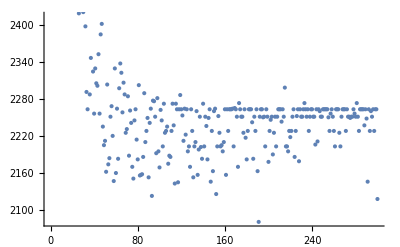

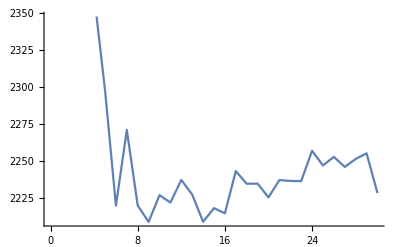

```mathematica
shortestPaths = {};
pathLengths = {};
paths = {};
Do[
Thread[{pl, p} = updateSimulation[]];
AppendTo[shortestPaths, Min[pl]];
AppendTo[pathLengths, pl];
AppendTo[paths, p]
, {i, 1, 300}];

ListPlot[shortestPaths]
ListPlot[Mean /@ Partition[shortestPaths, 10] , Joined->True]
```

```mathematica
shortestPaths // Min
```

2081

## Archive

numOfTowns = 30;
edges = Table[ RandomInteger[{1,10}] , {i, 1, numOfTowns}, {j, 1, numOfTowns}];
baseTrace = 0.01;
α=4;
β=1;
Q = 1;
ρ = 0.5;
300 runs

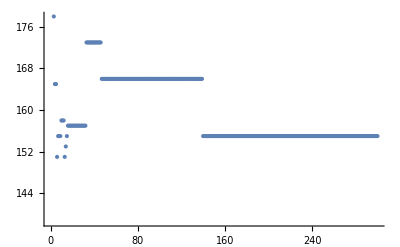
## 